```mathematica
Func20[x_]:=Module[{R1,R2},
R1 = Sin[(√13 x^3-9x-5-√17)/10];
R2 = Tan[(x^2+x+2^(1/3))/(3x-5)];
Return [R1 + R2 + 0.6]
];
Func23[x_]:=Module[{R1,R2},
R1 = Sin[(-2 x^2-√10 x+1)/4];
R2 = ((x^2+(√2+R1)*x - 3)/(R1*x - 3))^Log[2];
Return [R1 + R2 -1.2]
];
```

```mathematica
SetDirectory[NotebookDirectory[]];
namex20="output/vecx20.dat";
namey20 = "output/vecy20.dat";
namex23="output/vecx23.dat";
namey23 = "output/vecy23.dat";
x20 =Flatten@ Import[namex20];
y20 =Flatten@  Import[namey20];
x23 =Flatten@ Import[namex23];
y23 =Flatten@  Import[namey23];
points20=Table[{x20[[i]],y20[[i]]},{i,1,Length@x20}];
points23=Table[{x23[[i]],y23[[i]]},{i,1,Length@x23}];
```

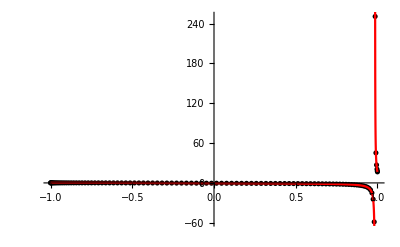

```mathematica
Discret20= ListPlot[points20,PlotRange->All,PlotStyle->{Black}];
Real20 = Plot[Func20[x],{x,-1,1},PlotStyle->{Red},PlotRange->All];
Show[Discret20,Real20]
```

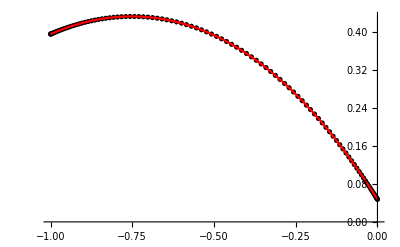

```mathematica
Discret23= ListPlot[points23,PlotRange->All,PlotStyle->{Black}];
Real23 = Plot[Func23[x],{x,-1,0},PlotStyle->{Red},PlotRange->All];
Show[Discret23,Real23]
```